```mathematica
(m+1)/(m-1)Integrate[1/(x^2+λ)1/(x^2+t^2)x^2,{x,0,R},Assumptions->λ>0&&t>0&&R>0]
```

((1+m) (√λ ArcTan[R/(√λ)]-ArcTan[R/(√λ_0)] √λ_0))/((-1+m) (λ-λ_0))

```mathematica
%/.{λ->(m+1)/(m-1)λ}
```

((1+m) (√(((1+m) λ)/(-1+m)) ArcTan[R/(√(((1+m) λ)/(-1+m)))]-ArcTan[R/(√((((1+m) λ)/(-1+m))_0))] √((((1+m) λ)/(-1+m))_0)))/((-1+m) (((1+m) λ)/(-1+m)-(((1+m) λ)/(-1+m))_0))

```mathematica
a:=((1+m) (√(((1+m) λ)/(-1+m)) ArcTan[R/(√(((1+m) λ)/(-1+m)))]-ArcTan[R/(√Subscript[((1+m) λ)/(-1+m), 0])] √Subscript[((1+m) λ)/(-1+m), 0]))/((-1+m) (((1+m) λ)/(-1+m)-Subscript[((1+m) λ)/(-1+m), 0]))
```

```mathematica
(m+1)/(m-1)Integrate[1/(x^2+λ)x^2,{x,0,R},Assumptions->λ>0&&Subscript[λ, 0]>0&&R>0]
```

((1+m) (R-√λ ArcTan[R/(√λ)]))/(-1+m)

```mathematica
%/.{λ->(m+1)/(m-1)λ}
```

((1+m) (R-√(((1+m) λ)/(-1+m)) ArcTan[R/(√(((1+m) λ)/(-1+m)))]))/(-1+m)

```mathematica
b:=((1+m) (R-√(((1+m) λ)/(-1+m)) ArcTan[R/(√(((1+m) λ)/(-1+m)))]))/(-1+m)
```

```mathematica
(m+1)/(m-1)Integrate[1/(x^2+λ)(1/(x^2+Subscript[λ, 0]))^2x^2,{x,0,R},Assumptions->λ>0&&Subscript[λ, 0]>0&&R>0]
```

((1+m) (-2 R^2 ArcTan[R/(√λ)] √(λ λ_0)-2 ArcTan[R/(√λ)] √(λ λ_0^3)+R √λ_0 (-λ+λ_0)+R^2 ArcTan[R/(√λ_0)] (λ+λ_0)+ArcTan[R/(√λ_0)] λ_0 (λ+λ_0)))/(2 (-1+m) (λ-λ_0)^2 √λ_0 (R^2+λ_0))

```mathematica
%/.{λ->(m+1)/(m-1)λ}
```

((1+m) (-2 R^2 ArcTan[R/(√(((1+m) λ)/(-1+m)))] √(((1+m) λ (((1+m) λ)/(-1+m))_0)/(-1+m))-2 ArcTan[R/(√(((1+m) λ)/(-1+m)))] √(((1+m) λ (((1+m) λ)/(-1+m))_0^3)/(-1+m))+R √((((1+m) λ)/(-1+m))_0) (-((1+m) λ)/(-1+m)+(((1+m) λ)/(-1+m))_0)+R^2 ArcTan[R/(√((((1+m) λ)/(-1+m))_0))] (((1+m) λ)/(-1+m)+(((1+m) λ)/(-1+m))_0)+ArcTan[R/(√((((1+m) λ)/(-1+m))_0))] (((1+m) λ)/(-1+m))_0 (((1+m) λ)/(-1+m)+(((1+m) λ)/(-1+m))_0)))/(2 (-1+m) (((1+m) λ)/(-1+m)-(((1+m) λ)/(-1+m))_0)^2 √((((1+m) λ)/(-1+m))_0) (R^2+(((1+m) λ)/(-1+m))_0))

```mathematica
%//Simplify
```

((1+m) ((1+m) R^2 λ ArcTan[R/(√((((1+m) λ)/(-1+m))_0))]-(1+m) R λ √((((1+m) λ)/(-1+m))_0)+((-1+m) R^2+(1+m) λ) ArcTan[R/(√((((1+m) λ)/(-1+m))_0))] (((1+m) λ)/(-1+m))_0+(-1+m) R (((1+m) λ)/(-1+m))_0^(3/2)+(-1+m) ArcTan[R/(√((((1+m) λ)/(-1+m))_0))] (((1+m) λ)/(-1+m))_0^2-2 (-1+m) ArcTan[R/(√(((1+m) λ)/(-1+m)))] (R^2 √(((1+m) λ (((1+m) λ)/(-1+m))_0)/(-1+m))+√(((1+m) λ (((1+m) λ)/(-1+m))_0^3)/(-1+m)))))/(2 √((((1+m) λ)/(-1+m))_0) (R^2+(((1+m) λ)/(-1+m))_0) ((1+m) λ-(-1+m) (((1+m) λ)/(-1+m))_0)^2)

```mathematica
(-2 R^2 ArcTan[R/(√λ)] √(λ Subscript[λ, 0])-2 ArcTan[R/(√λ)] √(λ Subscript[λ, 0]^3)+R √Subscript[λ, 0] (-λ+Subscript[λ, 0])+R^2 ArcTan[R/(√Subscript[λ, 0])] (λ+Subscript[λ, 0])+ArcTan[R/(√Subscript[λ, 0])] Subscript[λ, 0] (λ+Subscript[λ, 0]))/(2 (λ-Subscript[λ, 0])^2 √Subscript[λ, 0] (R^2+Subscript[λ, 0]))
c:=(-2 R^2 ArcTan[R/(√λ)] √(λ Subscript[λ, 0])-2 ArcTan[R/(√λ)] √(λ Subscript[λ, 0]^3)+R √Subscript[λ, 0] (-λ+Subscript[λ, 0])+R^2 ArcTan[R/(√Subscript[λ, 0])] (λ+Subscript[λ, 0])+ArcTan[R/(√Subscript[λ, 0])] Subscript[λ, 0] (λ+Subscript[λ, 0]))/(2 (λ-Subscript[λ, 0])^2 √Subscript[λ, 0] (R^2+Subscript[λ, 0]))
```

(-2 R^2 ArcTan[R/(√λ)] √(λ λ_0)-2 ArcTan[R/(√λ)] √(λ λ_0^3)+R √λ_0 (-λ+λ_0)+R^2 ArcTan[R/(√λ_0)] (λ+λ_0)+ArcTan[R/(√λ_0)] λ_0 (λ+λ_0))/(2 (λ-λ_0)^2 √λ_0 (R^2+λ_0))

```mathematica
c+χ/(4Pi R+α)4Pi(a/(1-4Pi χ/(4Pi R+α)b))a/.{Subscript[λ, 0]->t^2,λ->s^2}
```

(4 π χ (√(s^2) ArcTan[R/(√(s^2))]-√(t^2) ArcTan[R/(√(t^2))])^2)/((s^2-t^2)^2 (4 π R+α) (1-(4 π χ (R-√(s^2) ArcTan[R/(√(s^2))]))/(4 π R+α)))+(R √(t^2) (-s^2+t^2)-2 R^2 √(s^2 t^2) ArcTan[R/(√(s^2))]-2 √(s^2 t^6) ArcTan[R/(√(s^2))]+R^2 (s^2+t^2) ArcTan[R/(√(t^2))]+t^2 (s^2+t^2) ArcTan[R/(√(t^2))])/(2 √(t^2) (s^2-t^2)^2 (R^2+t^2))

```mathematica
Simplify[%,Assumptions->t>0&&s>0]
```

((R (-s^2+t^2))/(R^2+t^2)-2 s ArcTan[R/s]+(s^2/t+t) ArcTan[R/t]+(8 π χ (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α-4 π R (-1+χ)+4 π s χ ArcTan[R/s]))/(2 (s^2-t^2)^2)

```mathematica
%/.{ArcTan[R/t]->-α/(4Pi t)}
```

((R (-s^2+t^2))/(R^2+t^2)-((s^2/t+t) α)/(4 π t)-2 s ArcTan[R/s]+(8 π χ (α/(4 π)+s ArcTan[R/s])^2)/(α-4 π R (-1+χ)+4 π s χ ArcTan[R/s]))/(2 (s^2-t^2)^2)

```mathematica
Simplify[%,Assumptions->s>0&&t>0]
```

((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]+(8 π χ (α/(4 π)+s ArcTan[R/s])^2)/(α-4 π R (-1+χ)+4 π s χ ArcTan[R/s]))/(2 (s^2-t^2)^2)

```mathematica
D[%104,s]
```

1/(2 (s^2-t^2)^2)((2 R)/((1+R^2/s^2) s)-(2 R s)/(R^2+t^2)-(s α)/(2 π t^2)-2 ArcTan[R/s]-(8 π χ (α/(4 π)+s ArcTan[R/s])^2 (-(4 π R χ)/((1+R^2/s^2) s)+4 π χ ArcTan[R/s]))/(α-4 π R (-1+χ)+4 π s χ ArcTan[R/s])^2+(16 π χ (-R/((1+R^2/s^2) s)+ArcTan[R/s]) (α/(4 π)+s ArcTan[R/s]))/(α-4 π R (-1+χ)+4 π s χ ArcTan[R/s]))-(2 s ((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]+(8 π χ (α/(4 π)+s ArcTan[R/s])^2)/(α-4 π R (-1+χ)+4 π s χ ArcTan[R/s])))/((s^2-t^2)^3)

```mathematica
Limit[%104,R->Infinity]
```

-((4 π^2 t^2)/(√(1/s^2))+(s^2+t^2) α)/(8 π t^2 (s^2-t^2)^2)

```mathematica
Solve[%==0,s]
```

{{s→(-2 π^2 t^2-√(4 π^4 t^4-t^2 α^2))/α},{s→(2 π^2 t^2-√(4 π^4 t^4-t^2 α^2))/α},{s→(-2 π^2 t^2+√(4 π^4 t^4-t^2 α^2))/α},{s→(2 π^2 t^2+√(4 π^4 t^4-t^2 α^2))/α}}

```mathematica
Series[((8 π (√s ArcTan[R/(√s)]-√t ArcTan[R/(√t)])^2)/(α+4 π √s ArcTan[R/(√s)])+1/(√t (R^2+t))(R √t (-s+t)-2 (R^2 √(s t)+√(s t^3)) ArcTan[R/(√s)]+(R^2+t) (s+t) ArcTan[R/(√t)])),{s,t,2}]
```

(2 t (R^2+t) ArcTan[R/(√t)]-2 (R^2 √(t^2)+√(t^4)) ArcTan[R/(√t)])/(√t (R^2+t))+1/(t^(3/2) (R^2+t)^2)(R^2 t+t^2-R^2 √(t^2)-√(t^4)) (-R √t+R^2 ArcTan[R/(√t)]+t ArcTan[R/(√t)]) (s-t)+((8 π (-R/(2 (R^2+t))+ArcTan[R/(√t)]/(2 √t))^2)/(α+4 π √t ArcTan[R/(√t)])-1/(√t (R^2+t))2 (-(R (R^2 √(t^2)+√(t^4)))/(4 t^(3/2) (R^2+t))+((R^3+3 R t) (R^2 √(t^2)+√(t^4)))/(8 t^(3/2) (R^2+t)^2)+(-R^2/(8 √(t^2))-(√(t^4))/(8 t^2)) ArcTan[R/(√t)])) (s-t)^2+O[s-t]^3

```mathematica
Simplify[%,Assumptions->t>0]
```

(-(R^3+3 R t)/(4 t (R^2+t)^2)+R/(2 R^2 t+2 t^2)+ArcTan[R/(√t)]/(4 t^(3/2))+(2 π (R/(R^2+t)-ArcTan[R/(√t)]/(√t))^2)/(α+4 π √t ArcTan[R/(√t)])) (s-t)^2+O[s-t]^3

```mathematica
%/.{α->-4 π √t ArcTan[R/(√t)]}
```

Power::infy: Infinite expression 1/0 encountered.

(2 t (R^2+t) ArcTan[R/(√t)]-2 (R^2 √(t^2)+√(t^4)) ArcTan[R/(√t)])/(√t (R^2+t))+1/(t^(3/2) (R^2+t)^2)(R^2 t+t^2-R^2 √(t^2)-√(t^4)) (-R √t+R^2 ArcTan[R/(√t)]+t ArcTan[R/(√t)]) (s-t)+ComplexInfinity (s-t)^2+O[s-t]^3

```mathematica
%//Simplify
```

1/(2 (λ-λ_0)^2)((8 π (√λ ArcTan[R/(√λ)]-ArcTan[R/(√λ_0)] √λ_0)^2)/(α+4 π √λ ArcTan[R/(√λ)])+1/(√λ_0 (R^2+λ_0))(-2 R^2 ArcTan[R/(√λ)] √(λ λ_0)-2 ArcTan[R/(√λ)] √(λ λ_0^3)+R √λ_0 (-λ+λ_0)+R^2 ArcTan[R/(√λ_0)] (λ+λ_0)+ArcTan[R/(√λ_0)] λ_0 (λ+λ_0)))

```mathematica
Solve[%==0,λ]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1/(2 (λ-λ_0)^2)((8 π (√λ ArcTan[R/(√λ)]-ArcTan[R/(√λ_0)] √λ_0)^2)/(α+4 π √λ ArcTan[R/(√λ)])+1/(√λ_0 (R^2+λ_0))(-2 R^2 ArcTan[R/(√λ)] √(λ λ_0)-2 ArcTan[R/(√λ)] √(λ λ_0^3)+R √λ_0 (-λ+λ_0)+R^2 ArcTan[R/(√λ_0)] (λ+λ_0)+ArcTan[R/(√λ_0)] λ_0 (λ+λ_0)))==0,λ]

```mathematica
(8 π (√λ ArcTan[R/(√λ)]-ArcTan[R/(√Subscript[λ, 0])] √Subscript[λ, 0])^2)/(α+4 π √λ ArcTan[R/(√λ)])+1/(√Subscript[λ, 0] (R^2+Subscript[λ, 0]))(-2 R^2 ArcTan[R/(√λ)] √(λ Subscript[λ, 0])-2 ArcTan[R/(√λ)] √(λ Subscript[λ, 0]^3)+R √Subscript[λ, 0] (-λ+Subscript[λ, 0])+R^2 ArcTan[R/(√Subscript[λ, 0])] (λ+Subscript[λ, 0])+ArcTan[R/(√Subscript[λ, 0])] Subscript[λ, 0] (λ+Subscript[λ, 0]))/.{Subscript[λ, 0]->β}
```

```mathematica
(8 π (-√β ArcTan[R/(√β)]+√λ ArcTan[R/(√λ)])^2)/(α+4 π √λ ArcTan[R/(√λ)])+1/(√β (R^2+β))(R √β (β-λ)+R^2 (β+λ) ArcTan[R/(√β)]+β (β+λ) ArcTan[R/(√β)]-2 R^2 √(β λ) ArcTan[R/(√λ)]-2 √(β^3 λ) ArcTan[R/(√λ)])
```

```mathematica
Limit[(8 π (-√β ArcTan[R/(√β)]+√λ ArcTan[R/(√λ)])^2)/(α+4 π √λ ArcTan[R/(√λ)])+1/(√β (R^2+β))(R √β (β-λ)+R^2 (β+λ) ArcTan[R/(√β)]+β (β+λ) ArcTan[R/(√β)]-2 R^2 √(β λ) ArcTan[R/(√λ)]-2 √(β^3 λ) ArcTan[R/(√λ)]),R->Infinity]
```

(2 π^3 β (√(1/β)-√(1/λ))^2 λ)/(α+(2 π^2)/(√(1/λ)))-(π √(1/λ) √λ √(β λ))/(√β)+1/2 π √(1/β) (β+λ)

```mathematica
(2 π^3 β (√(1/β)-√(1/λ))^2 λ)/(α+(2 π^2)/(√(1/λ)))-(π √(1/λ) √λ √(β λ))/(√β)+1/2 π √(1/β) (β+λ)//.{λ->s^2}
```

(2 π^3 s^2 (-√(1/s^2)+√(1/β))^2 β)/((2 π^2)/(√(1/s^2))+α)-(π √(1/s^2) √(s^2) √(s^2 β))/(√β)+1/2 π √(1/β) (s^2+β)

```mathematica
FullSimplify[%,Assumptions->s>0]
```

-π s+(2 π^3 (-1+s √(1/β))^2 β)/(2 π^2 s+α)+1/2 π √(1/β) (s^2+β)

```mathematica
Solve[%==0,s]
```

{{s→-α/(6 π^2)+((-216 π^6-108 π^4 α √(1/β)-α^3 (1/β)^(3/2)-(18 π^2 α^2)/β)^(1/3))/(6 π^2 √(1/β))-(√(1/β) (-α^2-(12 π^2 α)/(√(1/β))-36 π^4 β))/(6 π^2 (-216 π^6-108 π^4 α √(1/β)-α^3 (1/β)^(3/2)-(18 π^2 α^2)/β)^(1/3))},{s→-α/(6 π^2)-((1+ⅈ √3) (-216 π^6-108 π^4 α √(1/β)-α^3 (1/β)^(3/2)-(18 π^2 α^2)/β)^(1/3))/(12 π^2 √(1/β))+((1-ⅈ √3) √(1/β) (-α^2-(12 π^2 α)/(√(1/β))-36 π^4 β))/(12 π^2 (-216 π^6-108 π^4 α √(1/β)-α^3 (1/β)^(3/2)-(18 π^2 α^2)/β)^(1/3))},{s→-α/(6 π^2)-((1-ⅈ √3) (-216 π^6-108 π^4 α √(1/β)-α^3 (1/β)^(3/2)-(18 π^2 α^2)/β)^(1/3))/(12 π^2 √(1/β))+((1+ⅈ √3) √(1/β) (-α^2-(12 π^2 α)/(√(1/β))-36 π^4 β))/(12 π^2 (-216 π^6-108 π^4 α √(1/β)-α^3 (1/β)^(3/2)-(18 π^2 α^2)/β)^(1/3))}}

```mathematica
Solve[%==0,λ]
```

$Aborted

```mathematica
%/.{λ->k*R^2}
```

(8 π (√(k R^2) ArcTan[R/(√(k R^2))]-√β ArcTan[R/(√β)])^2)/(α+4 π √(k R^2) ArcTan[R/(√(k R^2))])+1/(√β (R^2+β))(R √β (-k R^2+β)-2 R^2 √(k R^2 β) ArcTan[R/(√(k R^2))]-2 √(k R^2 β^3) ArcTan[R/(√(k R^2))]+R^2 (k R^2+β) ArcTan[R/(√β)]+β (k R^2+β) ArcTan[R/(√β)])

```mathematica
%//Simplify
```

(8 π (√(k R^2) ArcTan[R/(√(k R^2))]-√β ArcTan[R/(√β)])^2)/(α+4 π √(k R^2) ArcTan[R/(√(k R^2))])+1/(√β (R^2+β))(R √β (-k R^2+β)-2 (R^2 √(k R^2 β)+√(k R^2 β^3)) ArcTan[R/(√(k R^2))]+(R^2+β) (k R^2+β) ArcTan[R/(√β)])

```mathematica
%//Simplify
```

(8 π (√(k R^2) ArcTan[R/(√(k R^2))]-ArcTan[R/(√((k R^2)_0))] √((k R^2)_0))^2)/(α+4 π √(k R^2) ArcTan[R/(√(k R^2))])+(k R^4 ArcTan[R/(√((k R^2)_0))]-k R^3 √((k R^2)_0)+(1+k) R^2 ArcTan[R/(√((k R^2)_0))] ((k R^2)_0)+R ((k R^2)_0)^(3/2)+ArcTan[R/(√((k R^2)_0))] ((k R^2)_0)^2-2 ArcTan[R/(√(k R^2))] (R^2 √(k R^2 ((k R^2)_0))+√(k R^2 ((k R^2)_0)^3)))/(√((k R^2)_0) (R^2+(k R^2)_0))

```mathematica
Limit[(8 π (√(k R^2) ArcTan[R/(√(k R^2))]-√β ArcTan[R/(√β)])^2)/(α+4 π √(k R^2) ArcTan[R/(√(k R^2))])+1/(√β (R^2+β))(R √β (-k R^2+β)-2 (R^2 √(k R^2 β)+√(k R^2 β^3)) ArcTan[R/(√(k R^2))]+(R^2+β) (k R^2+β) ArcTan[R/(√β)]),R->Infinity]
```

DirectedInfinity[Sign[k] √(1/Sign[β])]

```mathematica
Limit[%,R->Infinity]
```

π/(2 √(1/β))+(2 π^3 β)/α

```mathematica
-α/(6 π^2)+((-216 π^6-108 π^4 α √(1/β)-α^3 (1/β)^(3/2)-(18 π^2 α^2)/β)^(1/3))/(6 π^2 √(1/β))-(√(1/β) (-α^2-(12 π^2 α)/(√(1/β))-36 π^4 β))/(6 π^2 (-216 π^6-108 π^4 α √(1/β)-α^3 (1/β)^(3/2)-(18 π^2 α^2)/β)^(1/3))//FullSimplify
```

(-α+((6 π^2+α √(1/β))^2)/(√(1/β) (-(18 π^2 α^2+(108 π^4 α)/(√(1/β))+α^3 √(1/β)+216 π^6 β)/β)^(1/3))+((-(18 π^2 α^2+(108 π^4 α)/(√(1/β))+α^3 √(1/β)+216 π^6 β)/β)^(1/3))/(√(1/β)))/(6 π^2)

```mathematica
%//.{β->t^2}
```

1/(6 π^2)(-α+((6 π^2+√(1/t^2) α)^2)/(√(1/t^2) (-(216 π^6 t^2+(108 π^4 α)/(√(1/t^2))+18 π^2 α^2+√(1/t^2) α^3)/t^2)^(1/3))+((-(216 π^6 t^2+(108 π^4 α)/(√(1/t^2))+18 π^2 α^2+√(1/t^2) α^3)/t^2)^(1/3))/(√(1/t^2)))

```mathematica
FullSimplify[%,t>0]
```

(36 π^4 t^2+12 π^2 t α+α^2-α (-(6 π^2 t+α)^3)^(1/3)+(-(6 π^2 t+α)^3)^(2/3))/(6 π^2 (-(6 π^2 t+α)^3)^(1/3))

```mathematica
%//.{(-(6 π^2 t+α)^3)^(1/3)->-(6 π^2 t+α),(-(6 π^2 t+α)^3)^(2/3)->(6 π^2 t+α)^2}
```

(36 π^4 t^2+12 π^2 t α-(-6 π^2 t-α) α+α^2+(6 π^2 t+α)^2)/(6 π^2 (-(6 π^2 t+α)^3)^(1/3))

```mathematica
Simplify[(36 π^4 t^2+12 π^2 t α-(-6 π^2 t-α) α+α^2+(6 π^2 t+α)^2)/(6 π^2 (-(6 π^2 t+α)^3)^(1/3))]
```

((4 π^2 t+α) (6 π^2 t+α))/(2 π^2 (-(6 π^2 t+α)^3)^(1/3))

```mathematica
(8 π (-√β ArcTan[R/(√β)]+√λ ArcTan[R/(√λ)])^2)/(α+4 π √λ ArcTan[R/(√λ)])+1/(√β (R^2+β))(R √β (β-λ)+R^2 (β+λ) ArcTan[R/(√β)]+β (β+λ) ArcTan[R/(√β)]-2 R^2 √(β λ) ArcTan[R/(√λ)]-2 √(β^3 λ) ArcTan[R/(√λ)])/.{λ->s^2,β->t^2}
```

(8 π (√(s^2) ArcTan[R/(√(s^2))]-√(t^2) ArcTan[R/(√(t^2))])^2)/(α+4 π √(s^2) ArcTan[R/(√(s^2))])+1/(√(t^2) (R^2+t^2))(R √(t^2) (-s^2+t^2)-2 R^2 √(s^2 t^2) ArcTan[R/(√(s^2))]-2 √(s^2 t^6) ArcTan[R/(√(s^2))]+R^2 (s^2+t^2) ArcTan[R/(√(t^2))]+t^2 (s^2+t^2) ArcTan[R/(√(t^2))])

```mathematica
Simplify[%,Assumptions->t>0&&s>0]
```

(R (-s^2+t^2))/(R^2+t^2)-2 s ArcTan[R/s]+(s^2/t+t) ArcTan[R/t]+(8 π (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+4 π s ArcTan[R/s])

```mathematica
(R (-s^2+t^2))/(R^2+t^2)-2 s ArcTan[R/s]+(s^2/t+t) ArcTan[R/t]+(8 π (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+4 π s ArcTan[R/s])/.{s->-2t-α/(2(Pi)^2)+r}
```

(R (t^2-(r-2 t-α/(2 π^2))^2))/(R^2+t^2)+(t+((r-2 t-α/(2 π^2))^2)/t) ArcTan[R/t]-2 (r-2 t-α/(2 π^2)) ArcTan[R/(r-2 t-α/(2 π^2))]+(8 π (-t ArcTan[R/t]+(r-2 t-α/(2 π^2)) ArcTan[R/(r-2 t-α/(2 π^2))])^2)/(α+4 π (r-2 t-α/(2 π^2)) ArcTan[R/(r-2 t-α/(2 π^2))])

```mathematica
Clear[R]
```

```mathematica
Manipulate[Manipulate[Manipulate[Plot[(R (t^2-(r-2 t-α/(2 π^2))^2))/(R^2+t^2)+(t+((r-2 t-α/(2 π^2))^2)/t) ArcTan[R/t]-2 (r-2 t-α/(2 π^2)) ArcTan[R/(r-2 t-α/(2 π^2))]+(8 π (-t ArcTan[R/t]+(r-2 t-α/(2 π^2)) ArcTan[R/(r-2 t-α/(2 π^2))])^2)/(α+4 π (r-2 t-α/(2 π^2)) ArcTan[R/(r-2 t-α/(2 π^2))]),{r,0.0001,3.2}],{R,1000,80000}],{t,1,2}],{α,-2,2}]
```

```mathematica
Limit[(R (t^2-(r-2 t-α/(2 π^2))^2))/(R^2+t^2)+(t+((r-2 t-α/(2 π^2))^2)/t) ArcTan[R/t]-2 (r-2 t-α/(2 π^2)) ArcTan[R/(r-2 t-α/(2 π^2))]+(8 π (-t ArcTan[R/t]+(r-2 t-α/(2 π^2)) ArcTan[R/(r-2 t-α/(2 π^2))])^2)/(α+4 π (r-2 t-α/(2 π^2)) ArcTan[R/(r-2 t-α/(2 π^2))]),R->Infinity]
```

-π/(√(1/((r-2 t-α/(2 π^2))^2)))+(8 π (π/(2 √(1/t^2))-π/(2 √(1/((r-2 t-α/(2 π^2))^2))))^2)/(α+1/(√(1/((-2 π^2 (r-2 t)+α)^2))))+1/2 π √(1/t^2) t (t+((r-2 t-α/(2 π^2))^2)/t)

```mathematica
%32/.{r->0}
```

-π/(√(1/((-2 t-α/(2 π^2))^2)))+(8 π (π/(2 √(1/t^2))-π/(2 √(1/((-2 t-α/(2 π^2))^2))))^2)/(α+1/(√(1/((4 π^2 t+α)^2))))+1/2 π √(1/t^2) t (t+((-2 t-α/(2 π^2))^2)/t)

```mathematica
FullSimplify[-π/(√(1/((-2 t-α/(2 π^2))^2)))+(8 π (π/(2 √(1/t^2))-π/(2 √(1/((-2 t-α/(2 π^2))^2))))^2)/(α+1/(√(1/((4 π^2 t+α)^2))))+1/2 π √(1/t^2) t (t+((-2 t-α/(2 π^2))^2)/t),Assumptions->t>0]
```

((2 π^2 t+α)^2 (1+√(1/((4 π^2 t+α)^2)) (4 π^2 t+α)))/(8 π^3 (t+t α √(1/((4 π^2 t+α)^2))))

```mathematica
%//Simplify
```

-2/(1+R^2/((r-2 t-α/(2 π^2))^2))-(2 R^2 (t^2-(r-2 t-α/(2 π^2))^2))/((R^2+t^2)^2)+(t^2-(r-2 t-α/(2 π^2))^2)/(R^2+t^2)+(t (t+((r-2 t-α/(2 π^2))^2)/t))/(R^2+t^2)-(32 π^2 (t ArcTan[R/t]-(r-2 t-α/(2 π^2)) ArcTan[R/(r-2 t-α/(2 π^2))])^2)/((1+R^2/((r-2 t-α/(2 π^2))^2)) (α+(4 π (r-2 t)-(2 α)/π) ArcTan[R/(r-2 t-α/(2 π^2))])^2)+(16 π (-t^2/(R^2+t^2)+1/(1+R^2/((r-2 t-α/(2 π^2))^2))) (-t ArcTan[R/t]+(r-2 t-α/(2 π^2)) ArcTan[R/(r-2 t-α/(2 π^2))]))/(α+(4 π (r-2 t)-(2 α)/π) ArcTan[R/(r-2 t-α/(2 π^2))])

```mathematica
FullSimplify[%27]
```

(2 R^2 (r-3 t) (r-t))/((R^2+t^2)^2)-(2 t^2)/(R^2+t^2)-(2 R^2 (r-2 t) α)/(π^2 (R^2+t^2)^2)+(R^2 α^2)/(2 π^4 (R^2+t^2)^2)-(2 π^2 (-2 π^2 (r-2 t)+α)^2 (α+4 π t ArcTan[R/t])^2)/((4 π^4 (R^2+(r-2 t)^2)-4 π^2 (r-2 t) α+α^2) (π α+(4 π^2 (r-2 t)-2 α) ArcTan[(2 π^2 R)/(2 π^2 (r-2 t)-α)])^2)-(4 π t^2 (α+4 π t ArcTan[R/t]))/((R^2+t^2) (-π α+2 (-2 π^2 (r-2 t)+α) ArcTan[(2 π^2 R)/(2 π^2 (r-2 t)-α)]))

```mathematica
%//FullSimplify
```

1/4 (-(2 α)/π-(R (2 π^2 t+α) (6 π^2 t+α))/(π^4 (R^2+t^2))+((4 π^4 t^2+8 π^2 t α+α^2) ArcTan[R/t])/(π^4 t)+(2 (α+4 π t ArcTan[R/t])^2)/(π α+2 (4 π^2 t+α) ArcTan[(2 π^2 R)/(4 π^2 t+α)]))

```mathematica
Limit[%,R->Infinity]
```

(-4 π^2 α+√(1/t^2) (4 π^4 t^2+8 π^2 t α+α^2)+(4 π^2 ((2 π^2)/(√(1/t^2))+α)^2)/(α+1/(√(1/((4 π^2 t+α)^2)))))/(8 π^3)

```mathematica
FullSimplify[(-4 π^2 α+√(1/t^2) (4 π^4 t^2+8 π^2 t α+α^2)+(4 π^2 ((2 π^2)/(√(1/t^2))+α)^2)/(α+1/(√(1/((4 π^2 t+α)^2)))))/(8 π^3),Assumptions->t>α/(4(Pi)^2)]
```

Piecewise[{{-((2 π^2 t+α)^2)/(4 π^3 t), t<0}, {((2 π^2 t+α) (4 π^2 t+α))/(8 π^3 t), 4 π^2 t+α≥0}, {0, True}}]

```mathematica
(R (-s^2+t^2))/(R^2+t^2)-2 s ArcTan[R/s]+(s^2/t+t) ArcTan[R/t]+(8 π (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+4 π s ArcTan[R/s])+(R (s^2-t^2))/(R^2+s^2)+(s+t^2/s) ArcTan[R/s]-2 t ArcTan[R/t]+(8 π (-s ArcTan[R/s]+t ArcTan[R/t])^2)/(α+4 π t ArcTan[R/t])//FullSimplify
```

(R (s-t) (s+t))/(R^2+s^2)+(R (-s^2+t^2))/(R^2+t^2)-2 s ArcTan[R/s]+(s+t^2/s) ArcTan[R/s]-2 t ArcTan[R/t]+(s^2/t+t) ArcTan[R/t]+(8 π (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+4 π s ArcTan[R/s])+(8 π (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+4 π t ArcTan[R/t])

```mathematica
D[%,s]
```

(2 R)/((1+R^2/s^2) s)-(2 R s)/(R^2+t^2)-2 ArcTan[R/s]+(2 s ArcTan[R/t])/t+(16 π (-R/((1+R^2/s^2) s)+ArcTan[R/s]) (s ArcTan[R/s]-t ArcTan[R/t]))/(α+4 π s ArcTan[R/s])-(8 π (-(4 π R)/((1+R^2/s^2) s)+4 π ArcTan[R/s]) (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+4 π s ArcTan[R/s])^2

```mathematica
Limit[(R (-s^2+t^2))/(R^2+t^2)-2 s ArcTan[R/s]+(s^2/t+t) ArcTan[R/t]+(8 π (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+4 π s ArcTan[R/s]),R->Infinity]
```

(√(1/t^2) (2 π^3 (s^2+(-3+(2 √(1/s^2))/(√(1/t^2))) t^2)+π (1/(√(1/s^2))-2/(√(1/t^2))+√(1/s^2) t^2) α))/(4 π^2+2 √(1/s^2) α)

```mathematica
FullSimplify[%,Assumptions->t>0&&s>0]
```

(π (s-t)^2 (2 π^2 (s+2 t)+α))/(2 t (2 π^2 s+α))

```mathematica
%/.{s->t}
```

0

```mathematica
(R (-s^2+t^2))/(R^2+t^2)-2 s ArcTan[R/s]+(s^2/t+t) ArcTan[R/t]+(8 π (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+4 π s ArcTan[R/s])/.{s->t}
```

0

```mathematica
Integrate[1/(x^2+t^2)x^2,{x,0,R}]
```

ConditionalExpression[R-t ArcTan[R/t], Im[t/R]>1||Im[t/R]<-1||Re[t/R]≠0]

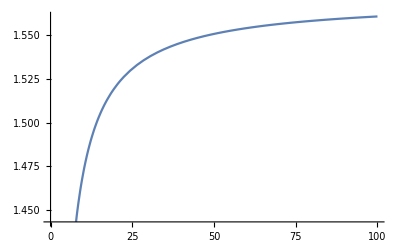

```mathematica
Plot[ArcTan[x],{x,0,100}]
```

```mathematica
Integrate[1/(k^2+s^2)1/(k^2+t^2)*k^2,{k,0,R},Assumptions->s>0&&t>0&&R>0]
```

(s ArcTan[R/s]-t ArcTan[R/t])/(s^2-t^2)

```mathematica
I1=4Pi*%
```

(4 π (s ArcTan[R/s]-t ArcTan[R/t]))/(s^2-t^2)

```mathematica
Integrate[1/(k^2+s^2)*k^2,{k,0,R},Assumptions->s>0&&t>0&&R>0]
```

R-s ArcTan[R/s]

```mathematica
I2=4Pi*%
```

4 π (R-s ArcTan[R/s])

```mathematica
Integrate[1/(k^2+s^2)(1/(k^2+t^2))^2*k^2,{k,0,R},Assumptions->s>0&&t>0&&R>0]
```

(R t (-s^2+t^2)+(R^2+t^2) (-2 s t ArcTan[R/s]+(s^2+t^2) ArcTan[R/t]))/(2 t (s^2-t^2)^2 (R^2+t^2))

```mathematica
I3=4Pi*%
```

(2 π (R t (-s^2+t^2)+(R^2+t^2) (-2 s t ArcTan[R/s]+(s^2+t^2) ArcTan[R/t])))/(t (s^2-t^2)^2 (R^2+t^2))

```mathematica
((m+1)/(m-1)1/(4Pi R+α)I1)/((m+1)/(m-1)+1/(4Pi R+α)I2)
```

(4 (1+m) π (s ArcTan[R/s]-t ArcTan[R/t]))/((-1+m) (s^2-t^2) (4 π R+α) ((1+m)/(-1+m)+(4 π (R-s ArcTan[R/s]))/(4 π R+α)))

```mathematica
A=%//Simplify
```

(4 (1+m) π (s ArcTan[R/s]-t ArcTan[R/t]))/((s^2-t^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))

```mathematica
I3-A*I1
```

-(16 (1+m) π^2 (s ArcTan[R/s]-t ArcTan[R/t])^2)/((s^2-t^2)^2 (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))+(2 π (R t (-s^2+t^2)+(R^2+t^2) (-2 s t ArcTan[R/s]+(s^2+t^2) ArcTan[R/t])))/(t (s^2-t^2)^2 (R^2+t^2))

```mathematica
%//Simplify
```

(2 π ((R (-s^2+t^2))/(R^2+t^2)-2 s ArcTan[R/s]+((s^2+t^2) ArcTan[R/t])/t-(8 (1+m) π (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])))/((s^2-t^2)^2)

```mathematica
%//FullSimplify
```

```mathematica
(2 π ((R (-s^2+t^2))/(R^2+t^2)-2 s ArcTan[R/s]+((s^2+t^2) ArcTan[R/t])/t-(8 (1+m) π (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])))/((s^2-t^2)^2)
```

(2 π ((R (-s^2+t^2))/(R^2+t^2)-2 s ArcTan[R/s]+((s^2+t^2) ArcTan[R/t])/t-(8 (1+m) π (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])))/((s^2-t^2)^2)

```mathematica
Series[2 π ((R (-s^2+t^2))/(R^2+t^2)-2 s ArcTan[R/s]+((s^2+t^2) ArcTan[R/t])/t-(8 (1+m) π (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])),{s,t,2}]
```

2 π ((2 R^3)/((R^2+t^2)^2)-R/(R^2+t^2)+ArcTan[R/t]/t-(8 (1+m) π (-(R t)/(R^2+t^2)+ArcTan[R/t])^2)/(α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t])) (s-t)^2+O[s-t]^3

```mathematica
Series[(s^2-t^2)^2,{s,t,2}]
```

4 t^2 (s-t)^2+O[s-t]^3

```mathematica
(2 R^3)/((R^2+t^2)^2)-R/(R^2+t^2)+ArcTan[R/t]/t-(8 (1+m) π (-(R t)/(R^2+t^2)+ArcTan[R/t])^2)/(α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t])
```

(2 R^3)/((R^2+t^2)^2)-R/(R^2+t^2)+ArcTan[R/t]/t-(8 (1+m) π (-(R t)/(R^2+t^2)+ArcTan[R/t])^2)/(α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t])

```mathematica
Collect[%,R]
```

(2 π ((R (-s^2+t^2))/(R^2+t^2)-2 s ArcTan[R/s]+((s^2+t^2) ArcTan[R/t])/t-(8 (1+m) π (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])))/((s^2-t^2)^2)

```mathematica
%/.{ArcTan[R/t]->-α/(4Pi*t)}
```

(2 π ((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-(8 (1+m) π (α/(4 π)+s ArcTan[R/s])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])))/((s^2-t^2)^2)

```mathematica
%305/.{ArcTan[R/s]->-α/(4Pi s)}
```

(2 π ((R (-s^2+t^2))/(R^2+t^2)+α/(2 π)-((s^2+t^2) α)/(4 π t^2)))/((s^2-t^2)^2)

```mathematica
Solve[(R (-s^2+t^2))/(R^2+t^2)+α/(2 π)-((s^2+t^2) α)/(4 π t^2)==0,s]
```

{{s→-(ⅈ √(4 π R t^2+R^2 α+t^2 α))/(2 √π √(R^2+t^2) √(-R/(R^2+t^2)-α/(4 π t^2)))},{s→(ⅈ √(4 π R t^2+R^2 α+t^2 α))/(2 √π √(R^2+t^2) √(-R/(R^2+t^2)-α/(4 π t^2)))}}

```mathematica
2 π ((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-(8 (1+m) π (α/(4 π)+s ArcTan[R/s])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))
```

2 π ((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-(8 (1+m) π (α/(4 π)+s ArcTan[R/s])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))

```mathematica
%//Together
```

(-32 m π^2 R^2 s^2 t^2+32 m π^2 R^2 t^4-8 m π R^3 s^2 α-8 m π R^3 t^2 α-4 π R s^2 t^2 α-12 m π R s^2 t^2 α+4 π R t^4 α-4 m π R t^4 α-R^2 s^2 α^2-m R^2 s^2 α^2-3 R^2 t^2 α^2-3 m R^2 t^2 α^2-s^2 t^2 α^2-m s^2 t^2 α^2-3 t^4 α^2-3 m t^4 α^2-64 m π^2 R^3 s t^2 ArcTan[R/s]-16 π^2 R s^3 t^2 ArcTan[R/s]+16 m π^2 R s^3 t^2 ArcTan[R/s]+16 π^2 R s t^4 ArcTan[R/s]-80 m π^2 R s t^4 ArcTan[R/s]-4 π R^2 s^3 α ArcTan[R/s]+4 m π R^2 s^3 α ArcTan[R/s]-28 π R^2 s t^2 α ArcTan[R/s]-20 m π R^2 s t^2 α ArcTan[R/s]-4 π s^3 t^2 α ArcTan[R/s]+4 m π s^3 t^2 α ArcTan[R/s]-28 π s t^4 α ArcTan[R/s]-20 m π s t^4 α ArcTan[R/s]-64 π^2 R^2 s^2 t^2 ArcTan[R/s]^2-64 π^2 s^2 t^4 ArcTan[R/s]^2)/(2 t^2 (R^2+t^2) (8 m π R+α+m α+4 π s ArcTan[R/s]-4 m π s ArcTan[R/s]))

```mathematica
Simplify[%290]
```

-((4 π R t^2+(R^2+t^2) α)^2+2 m (-8 π^2 R^2 t^2 (R^2-2 t^2)+2 π R (R^4+3 R^2 t^2+4 t^4) α+(R^2+t^2)^2 α^2))/(4 m π t^2 (R^2+t^2)^2 (4 π R+α))

```mathematica
Manipulate[Plot[-((4 π R t^2+(R^2+t^2) α)^2+2 m (-8 π^2 R^2 t^2 (R^2-2 t^2)+2 π R (R^4+3 R^2 t^2+4 t^4) α+(R^2+t^2)^2 α^2))/(4 m π t^2 (R^2+t^2)^2 (4 π R+α)),{t,-0.023183488476887844,0.023183488476887844}],{m,-11.,11.},{R,-2,2},{α,-2,2}]
```

```mathematica
FullSimplify[(4 π R t^2+(R^2+t^2) α)^2+2 m (-8 π^2 R^2 t^2 (R^2-2 t^2)+2 π R (R^4+3 R^2 t^2+4 t^4) α+(R^2+t^2)^2 α^2)]
```

(4 π R t^2+(R^2+t^2) α)^2+2 m (-8 π^2 R^2 t^2 (R^2-2 t^2)+2 π R (R^4+3 R^2 t^2+4 t^4) α+(R^2+t^2)^2 α^2)

```mathematica
%//FullSimplify
```

```mathematica
(2 π ((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-((1+m) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))))/((s^2-t^2)^2)/.{t->-α/(2Pi^2)+ϵ,s->t}
```

(2 π ((R (-t^2+(-α/(2 π^2)+ϵ)^2))/(R^2+(-α/(2 π^2)+ϵ)^2)-(α (t^2+(-α/(2 π^2)+ϵ)^2))/(4 π (-α/(2 π^2)+ϵ)^2)-2 t ArcTan[R/t]-((1+m) (α+4 π t ArcTan[R/t])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t]))))/((t^2-(-α/(2 π^2)+ϵ)^2)^2)

```mathematica
Solve[R+α/(4 π)-(π^3 t^2 α)/(α)^2-(4 π^4 R (R^2+t^2))/(α^2+4 π^4 (R^2))==0,t]
```

{{t→-(ⅈ √α √(4 π^4 R^2+4 π R α+α^2))/(2 √π √(4 π^4 R^2+α^2) √(-π^3/α-(4 π^4 R)/(4 π^4 R^2+α^2)))},{t→(ⅈ √α √(4 π^4 R^2+4 π R α+α^2))/(2 √π √(4 π^4 R^2+α^2) √(-π^3/α-(4 π^4 R)/(4 π^4 R^2+α^2)))}}

```mathematica
%//Simplify
```

(2 π ((R (-s^2+(-α/(2 π^2)+ϵ)^2))/(R^2+(-α/(2 π^2)+ϵ)^2)+(α (-1-(4 π^4 s^2)/((α-2 π^2 ϵ)^2)))/(4 π)-2 s ArcTan[R/s]-((1+m) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))))/((s^2-(-α/(2 π^2)+ϵ)^2)^2)

```mathematica
D[%,s]
```

(2 π ((2 R)/((1+R^2/s^2) s)-(2 π^3 s α)/((α-2 π^2 ϵ)^2)-(2 R s)/(R^2+(-α/(2 π^2)+ϵ)^2)-2 ArcTan[R/s]+((1+m) ((4 (-1+m) π R)/((1+R^2/s^2) s)-4 (-1+m) π ArcTan[R/s]) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)-((1+m) (-(4 π R)/((1+R^2/s^2) s)+4 π ArcTan[R/s]) (α+4 π s ArcTan[R/s]))/(π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))))/((s^2-(-α/(2 π^2)+ϵ)^2)^2)-(8 π s ((R (-s^2+(-α/(2 π^2)+ϵ)^2))/(R^2+(-α/(2 π^2)+ϵ)^2)+(α (-1-(4 π^4 s^2)/((α-2 π^2 ϵ)^2)))/(4 π)-2 s ArcTan[R/s]-((1+m) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))))/((s^2-(-α/(2 π^2)+ϵ)^2)^3)

```mathematica
Simplify[%150]
```

1/((s^2-(-α/(2 π^2)+ϵ)^2)^3)2 π (s (α/π+(4 π^3 s^2 α)/((α-2 π^2 ϵ)^2)-(4 R (-s^2+(-α/(2 π^2)+ϵ)^2))/(R^2+(-α/(2 π^2)+ϵ)^2)+8 s ArcTan[R/s]+(2 (1+m) (α+4 π s ArcTan[R/s])^2)/(π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])))+(s^2-(-α/(2 π^2)+ϵ)^2) ((2 R s)/(R^2+s^2)-(2 π^3 s α)/((α-2 π^2 ϵ)^2)-(2 R s)/(R^2+(-α/(2 π^2)+ϵ)^2)-2 ArcTan[R/s]-(2 (-1+m) (1+m) (α+4 π s ArcTan[R/s])^2 (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)-(4 (1+m) (α+4 π s ArcTan[R/s]) (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))))

```mathematica
FullSimplify[(s (α/π+(4 π^3 s^2 α)/((α-2 π^2 ϵ)^2)-(4 R (-s^2+(-α/(2 π^2)+ϵ)^2))/(R^2+(-α/(2 π^2)+ϵ)^2)+8 s ArcTan[R/s]+(2 (1+m) (α+4 π s ArcTan[R/s])^2)/(π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])))+(s^2-(-α/(2 π^2)+ϵ)^2) ((2 R s)/(R^2+s^2)-(2 π^3 s α)/((α-2 π^2 ϵ)^2)-(2 R s)/(R^2+(-α/(2 π^2)+ϵ)^2)-2 ArcTan[R/s]-(2 (-1+m) (1+m) (α+4 π s ArcTan[R/s])^2 (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)-(4 (1+m) (α+4 π s ArcTan[R/s]) (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))))]
```

s (α/π+(4 π^3 s^2 α)/((α-2 π^2 ϵ)^2)-(4 R (-s^2+(-α/(2 π^2)+ϵ)^2))/(R^2+(-α/(2 π^2)+ϵ)^2)+8 s ArcTan[R/s]+(2 (1+m) (α+4 π s ArcTan[R/s])^2)/(π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])))+(s^2-(-α/(2 π^2)+ϵ)^2) ((2 R s)/(R^2+s^2)-(2 π^3 s α)/((α-2 π^2 ϵ)^2)-(2 R s)/(R^2+(-α/(2 π^2)+ϵ)^2)-2 ArcTan[R/s]-(2 (-1+m^2) (α+4 π s ArcTan[R/s])^2 (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)-(4 (1+m) (α+4 π s ArcTan[R/s]) (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])))

```mathematica
Series[%,{ϵ,0,1}]
```

(2 π (-(R (4 π^4 s^2-α^2))/(4 π^4 R^2+α^2)-(π^3 (s^2+α^2/(4 π^4)))/α-2 s ArcTan[R/s]-((1+m) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))))/((s^2-α^2/(4 π^4))^2)+2 π ((-(4 π^5 s^2)/α^2-(16 π^6 R (R^2+s^2) α)/((4 π^4 R^2+α^2)^2))/((s^2-α^2/(4 π^4))^2)+(128 π^10 α (-(R (4 π^4 s^2-α^2))/(4 π^4 R^2+α^2)-(π^3 (s^2+α^2/(4 π^4)))/α-2 s ArcTan[R/s]-((1+m) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))))/((-4 π^4 s^2+α^2)^3)) ϵ+O[ϵ]^2

```mathematica
FullSimplify[(2 π (-(R (4 π^4 s^2-α^2))/(4 π^4 R^2+α^2)-(π^3 (s^2+α^2/(4 π^4)))/α-2 s ArcTan[R/s]-((1+m) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))))/((s^2-α^2/(4 π^4))^2),Assumptions->s>0]
```

(2 π (-(π^3 s^2)/α-α/(4 π)+(R (-4 π^4 s^2+α^2))/(4 π^4 R^2+α^2)-2 s ArcTan[R/s]-((1+m) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))))/((s^2-α^2/(4 π^4))^2)

```mathematica
Manipulate[Plot[((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-((1+m) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))),{s,t-0.1,t+0.1}],{m,1,30},{R,1,200},{t,-α/(2Pi^2),10},{α,-2,0}]
```

```mathematica
Limit[(2 π)/s^2 ((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-((1+m) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))),s->Infinity]
```

```mathematica
-(2 π R)/(R^2+t^2)-α/(2 t^2)//.{t->-α/(2Pi^2),α->-4.1,R->1}
```

41.4933

```mathematica
D[ ((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-((1+m) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))),R]
```

-2/(1+R^2/s^2)-(2 R^2 (-s^2+t^2))/((R^2+t^2)^2)+(-s^2+t^2)/(R^2+t^2)+((1+m) (8 m π-(4 (-1+m) π)/(1+R^2/s^2)) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)-(4 (1+m) (α+4 π s ArcTan[R/s]))/((1+R^2/s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))

```mathematica
%//Simplify
```

-(2 s^2)/(R^2+s^2)+(2 R^2 (s^2-t^2))/((R^2+t^2)^2)+(-s^2+t^2)/(R^2+t^2)+(2 (1+m) (s^2+m (2 R^2+s^2)) (α+4 π s ArcTan[R/s])^2)/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)-(4 (1+m) (α+4 π s ArcTan[R/s]))/((1+R^2/s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))

```mathematica
FindRoot[-t ArcTan[200/t]==-1.02/(4 π),{{t,0.1}}]
```

{t→0.0516823}

```mathematica
Limit[(-2 π^2 s+α)^2(2 π ((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-((1+m) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))))/((s^2-t^2)^2),t->-α/(2Pi^2)]
```

(2 π (-2 π^2 s+α)^2 ((R (-s^2+α^2/(4 π^4)))/(R^2+α^2/(4 π^4))-(π^3 (s^2+α^2/(4 π^4)))/α-2 s ArcTan[R/s]-((1+m) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))))/((s^2-α^2/(4 π^4))^2)

```mathematica
Limit[%,R->Infinity]
```

-(8 π^8 s^2 (2 π^2+√(1/s^2) α)^2)/(α (-4 π^4 s^2+α^2)^2)

```mathematica
Simplify[%,Assumptions->s>0]
```

-(8 π^8)/(α (-2 π^2 s+α)^2)

```mathematica
Manipulate[Plot[-((4 π^2 t^2)/(√(1/s^2))+(s^2+t^2) α)/(2 t^2 (s^2-t^2)^2),{s,0,1}],{m,1,30},{R,1,200},{t,-α/(2Pi^2),10},{α,-2,0}]
```

```mathematica
%//Simplify
```

(2 π (-(6 R)/(1+2 √(1+R^2/s^2))+(R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-((1+m) ((12 π R)/(1+2 √(1+R^2/s^2))+α)^2)/(2 π (-(12 (-1+m) π R)/(1+2 √(1+R^2/s^2))+α+m (8 π R+α)))))/((s^2-t^2)^2)

```mathematica
FullSimplify[%166,Assumptions->s>0&&R>0]
```

(2 π (-(6 R s)/(s+2 √(R^2+s^2))+(R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-((1+m) ((12 π R s)/(s+2 √(R^2+s^2))+α)^2)/(2 π (-(12 (-1+m) π R s)/(s+2 √(R^2+s^2))+α+m (8 π R+α)))))/((s^2-t^2)^2)

```mathematica
D[%170,s]
```

(2 π ((6 R s (1+(2 s)/(√(R^2+s^2))))/((s+2 √(R^2+s^2))^2)-(6 R)/(s+2 √(R^2+s^2))-(2 R s)/(R^2+t^2)-(s α)/(2 π t^2)+((1+m) ((12 (-1+m) π R s (1+(2 s)/(√(R^2+s^2))))/((s+2 √(R^2+s^2))^2)-(12 (-1+m) π R)/(s+2 √(R^2+s^2))) ((12 π R s)/(s+2 √(R^2+s^2))+α)^2)/(2 π (-(12 (-1+m) π R s)/(s+2 √(R^2+s^2))+α+m (8 π R+α))^2)-((1+m) (-(12 π R s (1+(2 s)/(√(R^2+s^2))))/((s+2 √(R^2+s^2))^2)+(12 π R)/(s+2 √(R^2+s^2))) ((12 π R s)/(s+2 √(R^2+s^2))+α))/(π (-(12 (-1+m) π R s)/(s+2 √(R^2+s^2))+α+m (8 π R+α)))))/((s^2-t^2)^2)-(8 π s (-(6 R s)/(s+2 √(R^2+s^2))+(R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-((1+m) ((12 π R s)/(s+2 √(R^2+s^2))+α)^2)/(2 π (-(12 (-1+m) π R s)/(s+2 √(R^2+s^2))+α+m (8 π R+α)))))/((s^2-t^2)^3)

```mathematica
%//Simplify
```

(2 π ((k (-s^2+t^2))/((1+k^2) t)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[(k t)/s]-((1+m) (α+4 π s ArcTan[(k t)/s])^2)/(2 π (8 k m π t+α+m α-4 (-1+m) π s ArcTan[(k t)/s]))))/((s^2-t^2)^2)

```mathematica
Limit[%,k->Infinity]
```

-(4 π^2 s^2 t √(t^2/s^2)+(s^2+t^2) α)/(2 (-s^2 t+t^3)^2)

```mathematica
Series[2 π ((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-((1+m) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))),{s,t,2}]
```

2 π (-α/(2 π)-2 t ArcTan[R/t]-((1+m) (α+4 π t ArcTan[R/t])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t])))+2 π (-(2 R t)/(R^2+t^2)-α/(2 π t)-2 (-(R t)/(R^2+t^2)+ArcTan[R/t])-(2 (1+m) (α+4 π t ArcTan[R/t]) (16 m π R+α+3 m α+4 π t ArcTan[R/t]-4 m π t ArcTan[R/t]) (-R t+R^2 ArcTan[R/t]+t^2 ArcTan[R/t]))/((R^2+t^2) (8 m π R+α+m α+4 π t ArcTan[R/t]-4 m π t ArcTan[R/t])^2)) (s-t)+2 π ((2 R^3)/((R^2+t^2)^2)-R/(R^2+t^2)-α/(4 π t^2)+((1+m) (-(32 (-1+m) π^2 (-(R t)/(R^2+t^2)+ArcTan[R/t])^2 (α+4 π t ArcTan[R/t]))/(α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t])^2-(16 π^2 (-(R t)/(R^2+t^2)+ArcTan[R/t])^2-(8 π R^3 (α+4 π t ArcTan[R/t]))/((R^2+t^2)^2))/(α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t])-((α+4 π t ArcTan[R/t])^2 ((16 (-1+m)^2 π^2 (-(R t)/(R^2+t^2)+ArcTan[R/t])^2)/(α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t])^2-(4 (-1+m) π R^3)/((R^2+t^2)^2 (α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t]))))/(α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t])))/(2 π)) (s-t)^2+O[s-t]^3

```mathematica
%/.{ArcTan[R/t]->-α/(4Pi*t)}
```

2 π (-(2 R t)/(R^2+t^2)-α/(2 π t)-2 (-(R t)/(R^2+t^2)-α/(4 π t))) (s-t)+2 π ((2 R^3)/((R^2+t^2)^2)-R/(R^2+t^2)-α/(4 π t^2)-(8 (1+m) π (-(R t)/(R^2+t^2)-α/(4 π t))^2)/(α+(-1+m) α+m (8 π R+α))) (s-t)^2+O[s-t]^3

```mathematica
%//Simplify
```

((4 π R^3)/((R^2+t^2)^2)-(2 π R)/(R^2+t^2)-α/(2 t^2)-((1+m) (4 π R t^2+(R^2+t^2) α)^2)/(2 m t^2 (R^2+t^2)^2 (4 π R+α))) (s-t)^2+O[s-t]^3

```mathematica
Limit[%,R->Infinity]
```

```mathematica
-((4 π^2 t^2)/(√(1/s^2))+(s^2+t^2) α)/(2 t^2 (s^2-t^2)^2)/.{t->-α/(2Pi^2)}
```

```mathematica
Simplify[-(2 π^4 (α^2/(π^2 √(1/s^2))+α (s^2+α^2/(4 π^4))))/(α^2 (s^2-α^2/(4 π^4))^2),Assumptions->s>0]
```

-(8 π^8)/(α (-2 π^2 s+α)^2)

```mathematica
Solve[%==0,s]
```

{}

```mathematica
%//Simplify
```

(2 π ((R (t^2-R^2 κ^2))/(R^2+t^2)-(α (t^2+R^2 κ^2))/(4 π t^2)-2 R κ ArcTan[1/κ]-((1+m) (α+4 π R κ ArcTan[1/κ])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π R κ ArcTan[1/κ]))))/((t^2-R^2 κ^2)^2)

```mathematica
Limit[%,m->Infinity]
```

-((32 π^2 R^2 s^2 t^2-32 π^2 R^2 t^4+8 π R^3 s^2 α+8 π R^3 t^2 α+12 π R s^2 t^2 α+4 π R t^4 α+R^2 s^2 α^2+3 R^2 t^2 α^2+s^2 t^2 α^2+3 t^4 α^2+64 π^2 R^3 s t^2 ArcTan[R/s]-16 π^2 R s^3 t^2 ArcTan[R/s]+80 π^2 R s t^4 ArcTan[R/s]-4 π R^2 s^3 α ArcTan[R/s]+20 π R^2 s t^2 α ArcTan[R/s]-4 π s^3 t^2 α ArcTan[R/s]+20 π s t^4 α ArcTan[R/s])/(2 t^2 (R^2+t^2) (-s^2+t^2)^2 (8 π R+α-4 π s ArcTan[R/s])))

```mathematica
FullSimplify[%80]
```

((4 π R (4 R^2-s^2+5 t^2))/(R^2+t^2)+(5-s^2/t^2) α-(8 (4 π R+α)^2)/(8 π R+α-4 π s ArcTan[R/s]))/(2 (s-t)^2 (s+t)^2)

(2 π ((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-(α+4 π s ArcTan[R/s])^2/(2 π (1+4 π R-4 π s ArcTan[R/s]))))/((s^2-t^2)^2)

```mathematica
Integrate[1/(k^2+t^2)k^2,{k,0,R},Assumptions->t>0&&R>0]
```

R-t ArcTan[R/t]

```mathematica
Solve[(4 π^2 t^2)/(√(1/s^2))+(s^2+t^2) α==0,s]
```

{{s→(-2 π^2 t^2-√(4 π^4 t^4-t^2 α^2))/α},{s→(2 π^2 t^2-√(4 π^4 t^4-t^2 α^2))/α},{s→(-2 π^2 t^2+√(4 π^4 t^4-t^2 α^2))/α},{s→(2 π^2 t^2+√(4 π^4 t^4-t^2 α^2))/α}}

```mathematica
Series[((4 π^2 t^2)/(√(1/s^2))+(s^2+t^2) α)/(2 t^2),{s,t,2}]
```

((2 π^2)/(√(1/t^2))+α)+(((4 π^2 t)/(√(1/t^2))+2 t α) (s-t))/(2 t^2)+(α (s-t)^2)/(2 t^2)+O[s-t]^3

```mathematica
R^3-((Integrate[1/(k^2+t^2)k^2,{k,0,R},Assumptions->t>0&&R>0])^2)/((Integrate[(1/(k^2+t^2))^2k^2,{k,0,R},Assumptions->t>0&&R>0])^2)
```

R^3-(4 (R-t ArcTan[R/t])^2)/((-R/(R^2+t^2)+ArcTan[R/t]/t)^2)

```mathematica
Limit[1/(4Pi R)(R^3-(4 (R-t ArcTan[R/t])^2)/((-R/(R^2+t^2)+ArcTan[R/t]/t)^2))^(1/2),R->Infinity]
```

∞

```mathematica
D[(2 π)/s^2((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-((1+m) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))),s]
```

(2 π ((2 R)/((1+R^2/s^2) s)-(2 R s)/(R^2+t^2)-(s α)/(2 π t^2)-2 ArcTan[R/s]+((1+m) ((4 (-1+m) π R)/((1+R^2/s^2) s)-4 (-1+m) π ArcTan[R/s]) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)-((1+m) (-(4 π R)/((1+R^2/s^2) s)+4 π ArcTan[R/s]) (α+4 π s ArcTan[R/s]))/(π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))))/s^2-(4 π ((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-((1+m) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))))/s^3

```mathematica
%//Simplify
```

(π ((4 R s^2)/(R^2+s^2)-(4 R s^2)/(R^2+t^2)+(4 R (s^2-t^2))/(R^2+t^2)-(s^2 α)/(π t^2)+((s^2+t^2) α)/(π t^2)+4 s ArcTan[R/s]+(2 (1+m) (α+4 π s ArcTan[R/s])^2)/(π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))-(4 (-1+m) (1+m) s (α+4 π s ArcTan[R/s])^2 (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)-(8 (1+m) s (α+4 π s ArcTan[R/s]) (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))))/s^3

```mathematica
%/.{s->t}
```

(π (α/π+4 t ArcTan[R/t]+(2 (1+m) (α+4 π t ArcTan[R/t])^2)/(π (α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t]))-(4 (-1+m) (1+m) t (α+4 π t ArcTan[R/t])^2 (-R t+(R^2+t^2) ArcTan[R/t]))/((R^2+t^2) (α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t])^2)-(8 (1+m) t (α+4 π t ArcTan[R/t]) (-R t+(R^2+t^2) ArcTan[R/t]))/((R^2+t^2) (α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t]))))/t^3

```mathematica
%//Simplify
```

```mathematica
(π (α/π+4 t ArcTan[R/t]+(2 (1+m) (α+4 π t ArcTan[R/t])^2)/(π (α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t]))-(4 (-1+m) (1+m) t (α+4 π t ArcTan[R/t])^2 (-R t+(R^2+t^2) ArcTan[R/t]))/((R^2+t^2) (α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t])^2)-(8 (1+m) t (α+4 π t ArcTan[R/t]) (-R t+(R^2+t^2) ArcTan[R/t]))/((R^2+t^2) (α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t]))))/t^3
```

(π (α/π+4 t ArcTan[R/t]+(2 (1+m) (α+4 π t ArcTan[R/t])^2)/(π (α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t]))-(4 (-1+m) (1+m) t (α+4 π t ArcTan[R/t])^2 (-R t+(R^2+t^2) ArcTan[R/t]))/((R^2+t^2) (α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t])^2)-(8 (1+m) t (α+4 π t ArcTan[R/t]) (-R t+(R^2+t^2) ArcTan[R/t]))/((R^2+t^2) (α+m (8 π R+α)-4 (-1+m) π t ArcTan[R/t]))))/t^3

```mathematica
%/.{t->-α/(2Pi^2)}
```

-(8 π^7 (α/π+(2 α ArcTan[(2 π^2 R)/α])/π^2+(2 (1+m) (α+(2 α ArcTan[(2 π^2 R)/α])/π)^2)/(π (α+m (8 π R+α)-(2 (-1+m) α ArcTan[(2 π^2 R)/α])/π))+(2 (-1+m) (1+m) α (α+(2 α ArcTan[(2 π^2 R)/α])/π)^2 ((R α)/(2 π^2)-(R^2+α^2/(4 π^4)) ArcTan[(2 π^2 R)/α]))/(π^2 (R^2+α^2/(4 π^4)) (α+m (8 π R+α)-(2 (-1+m) α ArcTan[(2 π^2 R)/α])/π)^2)+(4 (1+m) α (α+(2 α ArcTan[(2 π^2 R)/α])/π) ((R α)/(2 π^2)-(R^2+α^2/(4 π^4)) ArcTan[(2 π^2 R)/α]))/(π^2 (R^2+α^2/(4 π^4)) (α+m (8 π R+α)-(2 (-1+m) α ArcTan[(2 π^2 R)/α])/π))))/α^3

```mathematica
%//Simplify
```

-((8 π^5 (π+2 ArcTan[(2 π^2 R)/α]) (π^2 (α^2 (12 π^4 R^2+4 π R α+3 α^2)+2 m α (64 π^5 R^3+32 π^2 R^2 α+12 π^4 R^2 α+24 π R α^2+3 α^3)+m^2 (256 π^6 R^4+128 π^5 R^3 α+128 π^2 R^2 α^2+12 π^4 R^2 α^2+44 π R α^3+3 α^4))-2 π α (-16 m π R (4 π^4 R^2+α^2)-α (20 π^4 R^2+4 π R α+5 α^2)+m^2 (64 π^5 R^3+20 π^4 R^2 α+20 π R α^2+5 α^3)) ArcTan[(2 π^2 R)/α]-8 (-1+m) α^2 (4 π^4 R^2+α^2) ArcTan[(2 π^2 R)/α]^2))/(α^2 (4 π^4 R^2+α^2) (π (α+m (8 π R+α))-2 (-1+m) α ArcTan[(2 π^2 R)/α])^2))

```mathematica
Simplify[%248,Assumptions->α<0]
```

-((8 π^5 (π+2 ArcTan[(2 π^2 R)/α]) (π^2 (α^2 (12 π^4 R^2+4 π R α+3 α^2)+2 m α (64 π^5 R^3+32 π^2 R^2 α+12 π^4 R^2 α+24 π R α^2+3 α^3)+m^2 (256 π^6 R^4+128 π^5 R^3 α+128 π^2 R^2 α^2+12 π^4 R^2 α^2+44 π R α^3+3 α^4))-2 π α (-16 m π R (4 π^4 R^2+α^2)-α (20 π^4 R^2+4 π R α+5 α^2)+m^2 (64 π^5 R^3+20 π^4 R^2 α+20 π R α^2+5 α^3)) ArcTan[(2 π^2 R)/α]-8 (-1+m) α^2 (4 π^4 R^2+α^2) ArcTan[(2 π^2 R)/α]^2))/(α^2 (4 π^4 R^2+α^2) (π (α+m (8 π R+α))-2 (-1+m) α ArcTan[(2 π^2 R)/α])^2))

```mathematica
Limit[%,R->Infinity]
```

-(8 π^6 (1+√(1/α^2) α))/α^2

```mathematica
Manipulate[Plot[%243,{t,-8,8}],{m,1.001,8},{R,0.1,200},{α,-2,0}]
```

```mathematica
(2 π ((R (-s^2+t^2))/(R^2+t^2)-2 s ArcTan[R/s]+((s^2+t^2) ArcTan[R/t])/t-(8 (1+m) π (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])))/((s^2-t^2)^2)/.{ArcTan[R/t]->-α/(4Pi*t)}
```

(2 π ((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-(8 (1+m) π (α/(4 π)+s ArcTan[R/s])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])))/((s^2-t^2)^2)

```mathematica
Manipulate[Plot[2 π ((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-(8 (1+m) π (α/(4 π)+s ArcTan[R/s])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])),{s,0,1}],{m,1,3},{R,0.1,200},{t,-α/(2Pi^2),200},{α,-2,0}]
```

```mathematica
D[2 π ((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-(8 (1+m) π (α/(4 π)+s ArcTan[R/s])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])),s]
```

2 π ((2 R)/((1+R^2/s^2) s)-(2 R s)/(R^2+t^2)-(s α)/(2 π t^2)-2 ArcTan[R/s]+(8 (1+m) π ((4 (-1+m) π R)/((1+R^2/s^2) s)-4 (-1+m) π ArcTan[R/s]) (α/(4 π)+s ArcTan[R/s])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2-(16 (1+m) π (-R/((1+R^2/s^2) s)+ArcTan[R/s]) (α/(4 π)+s ArcTan[R/s]))/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))

```mathematica
D[α/(4Pi)+s^2/α Pi-Pi*s,s]
```

-π+(2 π s)/α

```mathematica
Solve[%==0,s]
```

{{s→α/2}}

```mathematica
α/(4Pi)+s^2/α Pi-Pi*s/.%
```

{α/(4 π)-(π α)/4}

```mathematica
%//Simplify
```

2 π ((4 R^3)/((R^2+s^2)^2)-(2 R)/(R^2+t^2)-α/(2 π t^2)+(4 (-1+m) (1+m) R^3 (α+4 π s ArcTan[R/s])^2)/((R^2+s^2)^2 (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)-(16 (1+m) π (-(R s)/(R^2+s^2)+ArcTan[R/s])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])+(8 (1+m) R^3 (α+4 π s ArcTan[R/s]))/((R^2+s^2)^2 (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))-(16 (-1+m)^2 (1+m) π (α+4 π s ArcTan[R/s])^2 (R s-(R^2+s^2) ArcTan[R/s])^2)/((R^2+s^2)^2 (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^3)-(32 (-1+m) (1+m) π (α+4 π s ArcTan[R/s]) (R s-(R^2+s^2) ArcTan[R/s])^2)/((R^2+s^2)^2 (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2))

```mathematica
D[2 π ((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-(8 (1+m) π (α/(4 π)+s ArcTan[R/s])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])),s]
```

2 π ((2 R)/((1+R^2/s^2) s)-(2 R s)/(R^2+t^2)-(s α)/(2 π t^2)-2 ArcTan[R/s]+(8 (1+m) π ((4 (-1+m) π R)/((1+R^2/s^2) s)-4 (-1+m) π ArcTan[R/s]) (α/(4 π)+s ArcTan[R/s])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2-(16 (1+m) π (-R/((1+R^2/s^2) s)+ArcTan[R/s]) (α/(4 π)+s ArcTan[R/s]))/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))

```mathematica
2 π ((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-(8 (1+m) π (α/(4 π)+s ArcTan[R/s])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))
```

2 π ((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-(8 (1+m) π (α/(4 π)+s ArcTan[R/s])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))

```mathematica
Limit[%,s->0]
```

```mathematica
(2 π R t^2)/(R^2+t^2)-α/2-((1+m) α^2)/(α+m (8 π R+α))/.{α->-2,R->20,m->1,t->0.1}
```

0.987098

```mathematica
%/.{ArcTan[R/s]->-α/(4Pi s)}
```

2 π ((4 R^3)/((R^2+s^2)^2)-(2 R)/(R^2+t^2)-α/(2 π t^2)-(16 (1+m) π (-(R s)/(R^2+s^2)-α/(4 π s))^2)/(α+(-1+m) α+m (8 π R+α)))

```mathematica
%/.{s->t}
```

2 π ((4 R^3)/((R^2+t^2)^2)-(2 R)/(R^2+t^2)-α/(2 π t^2)-(16 (1+m) π (-(R t)/(R^2+t^2)-α/(4 π t))^2)/(α+(-1+m) α+m (8 π R+α)))

```mathematica
%//Simplify
```

(8 π R^3)/((R^2+t^2)^2)-(4 π R)/(R^2+t^2)-α/t^2-((1+m) (4 π R t^2+(R^2+t^2) α)^2)/(m t^2 (R^2+t^2)^2 (4 π R+α))

```mathematica
D[%,s]
```

(4 π R)/((1+R^2/s^2) s^2)-(8 π R s^2)/((R^2+s^2)^2)+(4 π R)/(R^2+s^2)-(4 π R)/(R^2+t^2)-α/t^2-(4 (-1+m) (1+m) π (-R-(R (R^2+s^2))/((1+R^2/s^2) s^2)+2 s ArcTan[R/s]) (α+4 π s ArcTan[R/s])^2)/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)-(8 (1+m) π (-R-(R (R^2+s^2))/((1+R^2/s^2) s^2)+2 s ArcTan[R/s]) (α+4 π s ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))+(8 (-1+m) (1+m) π ((4 (-1+m) π R)/((1+R^2/s^2) s)-4 (-1+m) π ArcTan[R/s]) (α+4 π s ArcTan[R/s])^2 (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^3)-(8 (-1+m) (1+m) π (-(4 π R)/((1+R^2/s^2) s)+4 π ArcTan[R/s]) (α+4 π s ArcTan[R/s]) (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)+(8 (1+m) π ((4 (-1+m) π R)/((1+R^2/s^2) s)-4 (-1+m) π ArcTan[R/s]) (α+4 π s ArcTan[R/s]) (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)+(8 (-1+m) (1+m) π s (α+4 π s ArcTan[R/s])^2 (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2)^2 (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)-(8 (1+m) π (-(4 π R)/((1+R^2/s^2) s)+4 π ArcTan[R/s]) (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))+(16 (1+m) π s (α+4 π s ArcTan[R/s]) (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2)^2 (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))

```mathematica
%//FullSimplify
```

```mathematica
(4 π R s)/(R^2+s^2)-(4 π R s)/(R^2+t^2)-(s α)/t^2-4 π ArcTan[R/s]-(4 (-1+m^2) π (α+4 π s ArcTan[R/s])^2 (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)-(8 (1+m) π (α+4 π s ArcTan[R/s]) (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))
```

```mathematica
2 π ((R (-s^2+t^2))/(R^2+t^2)-2 s ArcTan[R/s]+((s^2+t^2) ArcTan[R/t])/t-(8 (1+m) π (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))
```

2 π ((R (-s^2+t^2))/(R^2+t^2)-2 s ArcTan[R/s]+((s^2+t^2) ArcTan[R/t])/t-(8 (1+m) π (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))

```mathematica
D[2 π ((R (-s^2+t^2))/(R^2+t^2)-2 s ArcTan[R/s]+((s^2+t^2) ArcTan[R/t])/t-(8 (1+m) π (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])),α]
```

(16 (1+m)^2 π^2 (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2

```mathematica
2 π ((R (-s^2+t^2))/(R^2+t^2)-2 s ArcTan[R/s]+((s^2+t^2) ArcTan[R/t])/t-(8 (1+m) π (s ArcTan[R/s]-t ArcTan[R/t])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))/.α->0
```

```mathematica
D[2 π ((R (-s^2+t^2))/(R^2+t^2)-2 s ArcTan[R/s]+((s^2+t^2) ArcTan[R/t])/t-(8 (1+m) π (s ArcTan[R/s]-t ArcTan[R/t])^2)/(8 m π R-4 (-1+m) π R)) ,s]
```

2 π ((2 R)/((1+R^2/s^2) s)-(2 R s)/(R^2+t^2)-2 ArcTan[R/s]+(2 s ArcTan[R/t])/t-(16 (1+m) π (-R/((1+R^2/s^2) s)+ArcTan[R/s]) (s ArcTan[R/s]-t ArcTan[R/t]))/(-4 (-1+m) π R+8 m π R))

```mathematica
%//Simplify
```

4 π ((R s)/(R^2+s^2)-(R s)/(R^2+t^2)-ArcTan[R/s]+(s ArcTan[R/t])/t-(2 (-R s+(R^2+s^2) ArcTan[R/s]) (s ArcTan[R/s]-t ArcTan[R/t]))/(R (R^2+s^2)))

```mathematica
%//FullSimplify
```

4 π ((R s)/(R^2+s^2)-(R s)/(R^2+t^2)-ArcTan[R/s]+(s ArcTan[R/t])/t-(2 (-R s+(R^2+s^2) ArcTan[R/s]) (s ArcTan[R/s]-t ArcTan[R/t]))/(R (R^2+s^2)))

```mathematica
t*%//Expand//FullSimplify
```

4 π (R s t (1/(R^2+s^2)-1/(R^2+t^2))+(-2 s (R^2+s^2) t ArcTan[R/s]^2+R s (R^2+s^2-2 t^2) ArcTan[R/t]+t ArcTan[R/s] (-R^3+R s^2+2 (R^2+s^2) t ArcTan[R/t]))/(R (R^2+s^2)))

```mathematica
Series[-2 s ArcTan[R/s]-(8 (1+m) π (α/(4 π)+s ArcTan[R/s])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]),{s,0,1}]
```

((-1)^Floor[(π-Arg[R^2]+2 Arg[s])/(2 π)] O[s]^3+(-1)^Floor[(π-Arg[R^2]+2 Arg[s])/(2 π)] (-(2 (π √(R^2) α) s)/R+O[s]^2)+(-1)^Floor[(π-Arg[R^2]+2 Arg[s])/(2 π)] (-(2 (m π √(R^2) α) s)/R+O[s]^2)+((-α^2-m α^2)/(2 π)+O[s]^2)+(-1)^Floor[(π-Arg[R^2]+2 Arg[s])/(2 π)] (-(π √(R^2) (α+m (8 π R+α)) s)/R+O[s]^2))/((-1)^Floor[(π-Arg[R^2]+2 Arg[s])/(2 π)] (-(2 ((-1+m) π^2 √(R^2)) s)/R+O[s]^2)+((α+m (8 π R+α))+O[s]^2))

```mathematica
%//Simplify
```

Piecewise[{{-((1+m) α^2)/(2 (π (α+m (8 π R+α))))+(2 π √(R^2) (α^2+2 m^2 (4 π R+α)^2+m α (16 π R+3 α)) s)/(R (α+m (8 π R+α))^2)+O[s]^2, Arg[R^2]>π+2 Arg[s]||π+Arg[R^2]≤2 Arg[s]}, {-((1+m) α^2)/(2 (π (α+m (8 π R+α))))-(2 (π √(R^2) (α^2+2 m^2 (4 π R+α)^2+m α (16 π R+3 α))) s)/(R (α+m (8 π R+α))^2)+O[s]^2, True}}]

```mathematica
2 π ((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-(8 (1+m) π (α/(4 π)+s ArcTan[R/s])^2)/(α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))
```

```mathematica
D[((R (-s^2+t^2))/(R^2+t^2)-((s^2+t^2) α)/(4 π t^2)-2 s ArcTan[R/s]-((1+m) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))),s]
```

(2 R)/((1+R^2/s^2) s)-(2 R s)/(R^2+t^2)-(s α)/(2 π t^2)-2 ArcTan[R/s]+((1+m) ((4 (-1+m) π R)/((1+R^2/s^2) s)-4 (-1+m) π ArcTan[R/s]) (α+4 π s ArcTan[R/s])^2)/(2 π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)-((1+m) (-(4 π R)/((1+R^2/s^2) s)+4 π ArcTan[R/s]) (α+4 π s ArcTan[R/s]))/(π (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))

```mathematica
%//Simplify
```

(2 R s)/(R^2+s^2)-(2 R s)/(R^2+t^2)-(s α)/(2 π t^2)-2 ArcTan[R/s]-(2 (-1+m) (1+m) (α+4 π s ArcTan[R/s])^2 (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)-(4 (1+m) (α+4 π s ArcTan[R/s]) (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))

```mathematica
%3//FullSimplify
```

(2 R s)/(R^2+s^2)-(2 R s)/(R^2+t^2)-(s α)/(2 π t^2)-2 ArcTan[R/s]-(2 (-1+m^2) (α+4 π s ArcTan[R/s])^2 (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)-(4 (1+m) (α+4 π s ArcTan[R/s]) (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))

```mathematica
D[%,s]
```

(2 R)/((1+R^2/s^2) s^2)-(4 R s^2)/((R^2+s^2)^2)+(2 R)/(R^2+s^2)-(2 R)/(R^2+t^2)-α/(2 π t^2)-(2 (-1+m) (1+m) (-R-(R (R^2+s^2))/((1+R^2/s^2) s^2)+2 s ArcTan[R/s]) (α+4 π s ArcTan[R/s])^2)/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)-(4 (1+m) (-R-(R (R^2+s^2))/((1+R^2/s^2) s^2)+2 s ArcTan[R/s]) (α+4 π s ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))+(4 (-1+m) (1+m) ((4 (-1+m) π R)/((1+R^2/s^2) s)-4 (-1+m) π ArcTan[R/s]) (α+4 π s ArcTan[R/s])^2 (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^3)-(4 (-1+m) (1+m) (-(4 π R)/((1+R^2/s^2) s)+4 π ArcTan[R/s]) (α+4 π s ArcTan[R/s]) (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)+(4 (1+m) ((4 (-1+m) π R)/((1+R^2/s^2) s)-4 (-1+m) π ArcTan[R/s]) (α+4 π s ArcTan[R/s]) (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)+(4 (-1+m) (1+m) s (α+4 π s ArcTan[R/s])^2 (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2)^2 (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)-(4 (1+m) (-(4 π R)/((1+R^2/s^2) s)+4 π ArcTan[R/s]) (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))+(8 (1+m) s (α+4 π s ArcTan[R/s]) (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2)^2 (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))

```mathematica
%//Simplify
```

-(4 R s^2)/((R^2+s^2)^2)+(4 R)/(R^2+s^2)-(2 R)/(R^2+t^2)-α/(2 π t^2)+(4 (-1+m) (1+m) (R-s ArcTan[R/s]) (α+4 π s ArcTan[R/s])^2)/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)+(8 (1+m) (R-s ArcTan[R/s]) (α+4 π s ArcTan[R/s]))/((R^2+s^2) (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))-(16 (-1+m)^2 (1+m) π (α+4 π s ArcTan[R/s])^2 (R s-(R^2+s^2) ArcTan[R/s])^2)/((R^2+s^2)^2 (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^3)-(32 (-1+m) (1+m) π (α+4 π s ArcTan[R/s]) (R s-(R^2+s^2) ArcTan[R/s])^2)/((R^2+s^2)^2 (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)-(16 (1+m) π (R s-(R^2+s^2) ArcTan[R/s])^2)/((R^2+s^2)^2 (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))+(4 (-1+m) (1+m) s (α+4 π s ArcTan[R/s])^2 (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2)^2 (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^2)+(8 (1+m) s (α+4 π s ArcTan[R/s]) (-R s+(R^2+s^2) ArcTan[R/s]))/((R^2+s^2)^2 (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s]))

```mathematica
FullSimplify[%]
```

(4 R^3)/((R^2+s^2)^2)-(2 R)/(R^2+t^2)-α/(2 π t^2)-(16 (-1+m)^2 (1+m) π R^2 s^2 α^2)/((R^2+s^2)^2 (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^3)+(4 (1+m) (R^2 (-32 m π^2 R s^2+4 π (4 m R^2+s^2-3 m s^2) α+(1+3 m) R α^2) (α+m (8 π R+α))+4 π R s (128 m^2 π^2 R^2 (2 R^2+s^2)+16 m π R ((3+5 m) R^2+4 m s^2) α+((3+m (6+7 m)) R^2+8 m^2 s^2) α^2) ArcTan[R/s]-16 π (8 m π^2 R^2 (2 m R^4+(-3+7 m) R^2 s^2+2 m s^4)+π R (8 m^2 R^4+(-3+19 m^2) R^2 s^2+8 m^2 s^4) α+m^2 (R^2+s^2)^2 α^2) ArcTan[R/s]^2+64 (-1+m)^2 π^3 R^3 s^3 ArcTan[R/s]^3))/((R^2+s^2)^2 (α+m (8 π R+α)-4 (-1+m) π s ArcTan[R/s])^3)